```mathematica
(* definition of the spiral Archimedean *)
```

```mathematica
a = 18; b=0.5;
r[ϕ_]:= a + b ϕ
```

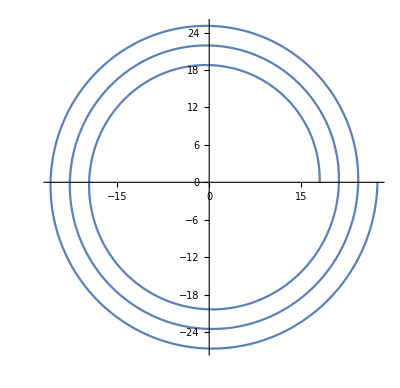

```mathematica
PolarPlot[r[ϕ],{ϕ,0,6 π}]
```

```mathematica
v= 600; (* linear velocity *)
```

```mathematica
Clear[ω]
```

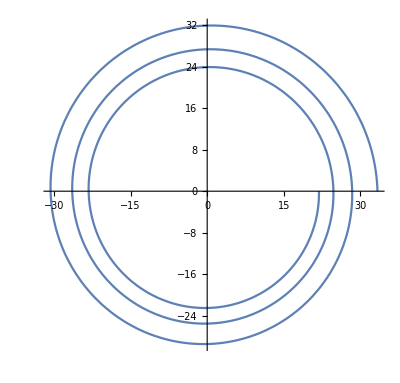

```mathematica
ω[ϕ_]:= v/r[ϕ];
PolarPlot[ω[ϕ], {ϕ,0,6 π}]
```

```mathematica
(* length  of the curve *)
```

```mathematica
ℒ =∫r[ϕ]ⅆϕ
```

18 ϕ+0.25 ϕ^2

```mathematica
% /.ϕ->6π/180
```

1.8877

```mathematica
pts =Table[{ϕ,r[ϕ]},{ϕ,0,6π, 6π/180}];
```

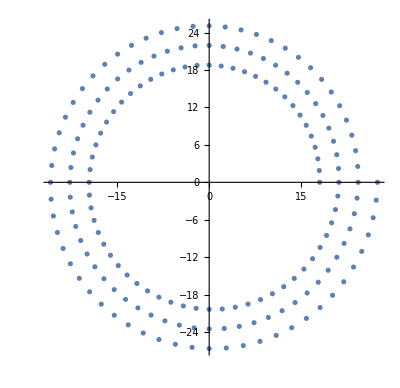

```mathematica
ListPolarPlot[pts]
```

This is now looking like good point cloud for the modeling. We transform the points in time series.

```mathematica
ptsTS = Table[{ϕ,r[ϕ],ϕ/ω[ϕ]},{ϕ,0,6π, 6π/180}];
```

```mathematica
(ℒ/.ϕ->6π/180)/ptsTS[[2]][[1]] (*this should be close to linear vel*)
```

599.13

Write the points to t-series file:

```mathematica
convertXYZ[pts_]:= Module[{ϕ = pts[[All,1]], r= pts[[All,2]], t=pts[[All,3]] // Partition[#,1]&},
x= r*Cos[ϕ];y=r*Sin[ϕ]; 
z=Table[{26}, {Length[pts]}]; power = Table[{40000},{Length[pts]}]; dia = Table[{0.2},{Length[pts]}];
Join[t,Partition[Riffle[x,y],2],z,power,dia,2]
]
```

```mathematica
Export["SpiralArchimedean.inp",convertXYZ[ptsTS],"CSV"]
```

SpiralArchimedean.inp

```mathematica
ptsTS[[2]]
```

{π/30,18.0524,0.00315073}